# Лабораторная работа №5

## Численное дифференцирование и интегрирование

Михалькевич Д.Н.
гр. 221701

Вариант 8

## Задание 1.

### Решить задачу Коши для дифференциального уравнения первого порядка на отрезке [0,1]:

#### а) методом Эйлера-Коши с шагом h_1 = 0.1, h_2=0.05, построить графики полученных решений

```mathematica
f[x_,y_]:=y^2+2x;
h1=0.1;
xe[0]=0;
ye[0]=0.3;
xe[i_]:= xe[i]=xe[i-1]+h1;
ye[i_]:=ye[i]= ye[i-1]+h1*f[xe[i-1],ye[i-1]];
```

```mathematica
xlist = Table[xe[i],{i,0,1/h1}]
ylist = Table[ye[i],{i,0,1/h1}]
```

{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{0.3,0.309,0.338548,0.39001,0.46522,0.566863,0.698997,0.867856,1.08317,1.3605,1.7256}

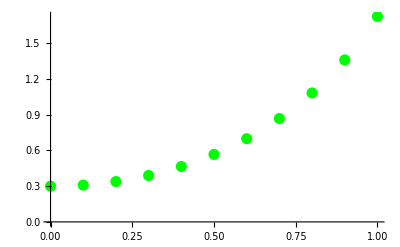

```mathematica
graph1=ListPlot[Transpose[{xlist,ylist}],PlotStyle->{PointSize[0.02],Green}]
```

```mathematica
f[x_,y_]:=y^2+2x;
h2=0.05;
xe2[0]=0;
ye2[0]=0.3;
xe2[i_]:=xe2[i]=xe2[i-1]+h2;
ye2[i_]:=ye2[i]= ye2[i-1]+h2*f[xe[i-1],ye[i-1]];
```

```mathematica
xlist2 = Table[xe2[i],{i,0,1/h2}]
ylist2 = Table[ye2[i],{i,0,1/h2}]
```

{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

{0.3,0.3045,0.319274,0.345005,0.38261,0.433432,0.499498,0.583928,0.691587,0.83025,1.0128,1.26168,1.61885,2.17035,3.11672,5.01701,9.90456,29.0948,196.825,7933.25,1.25947×10^7}

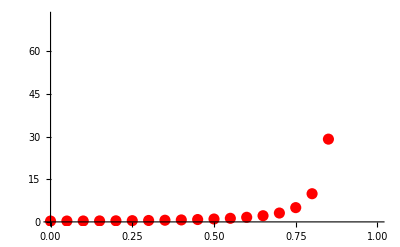

```mathematica
graph2=ListPlot[Transpose[{xlist2,ylist2}],PlotStyle->{PointSize[0.02],Red}]
```

```mathematica
Clear[y];
sol = NDSolve[{y'[x]==f[x,y[x]],y[0]==0.3},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[y[x]/. sol],{x,0,1},PlotRange->All]
```

-Graphics-

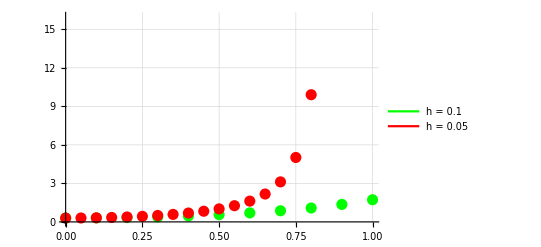

```mathematica
Legended[Show[graph1,graph2,Plot[Evaluate[y[x]/. sol],{x,0,1},PlotRange->All],GridLines->Automatic,PlotRange->{{0,1},{0,16}}],LineLegend[{Green,Red},{"h = 0.1","h = 0.05"}]]
```

#### б) методом Рунге - Кутта 4 - го порядка с шагом h1 = 0, 1 и h2 = 0, 05, построить графики полученных решений;

```mathematica
Clear[x,y]
```

```mathematica
sol1=List[{xe,ye}];
x=xe;y=ye;
For[k=1,k<n+1,k++,k1[x_,y_]=h*f[x,y];
k2[x_,y_]=h*f[x+h/2.0,y+k1[x,y]/2.0];
k3[x_,y_]=h*f[x+h/2.0,y+k2[x,y]/2.0];
k4[x_,y_]=h*f[x+h,y+k3[x,y]];
x=x+h;y=y+(k1[x,y]+2.0*k2[x,y]+2.0*k3[x,y]+k4[x,y])/6.0;
sol1=Append[sol1,{x,y}]]
sol1
```

{{xe,ye}}

```mathematica
gr6=ListPlot[sol1,PlotStyle->Green]
```

-Graphics-